```mathematica
wpe[n_,m_,q_]:=Sqrt[n q^2/(m ϵ0)];
wce[Z_,m_,q_]:=Abs[Z] q b0 /m;
ζ[vTh_,k_,ω_]:=ω/(k vTh);
Z[x_]:= I Sqrt[Pi] Exp[-x^2] Erfc[-I x];
(*Z[x_]:= I Sqrt[Pi] Exp[-x^2] (1+Erfi[-I x/I]/I);*)
Zp[x_]:=-2 (1+x Z[x]);
K3[vTh_,k_,ω_,n_,m_,q_]=FullSimplify[1-wpe[n,m,q]^2/(ω k vTh) Sum[BesselI[b,0] ζ[vTh,k,ω] Zp[ζ[vTh,k,ω]],{b,0,0}]];
sig33[vTh_,ω_,ϵ0_,k_,n_,m_,q_]=Simplify[-(K3[vTh,k,ω,n,m,q]-1) I ω ϵ0]
stixP=1-wpe[n,m,q]^2/ω^2;
sig33Cold=-(stixP-1) I ω ϵ0
```

-(2 ⅈ n q^2 ω (k vTh+ⅈ ⅇ^(-ω^2/(k^2 vTh^2)) √π ω Erfc[-(ⅈ ω)/(k vTh)]))/(k^3 m vTh^3)

(ⅈ n q^2)/(m ω)

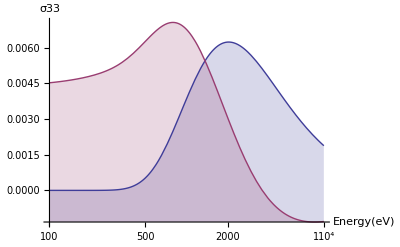

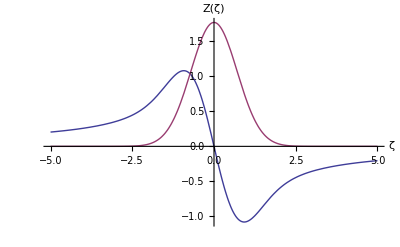

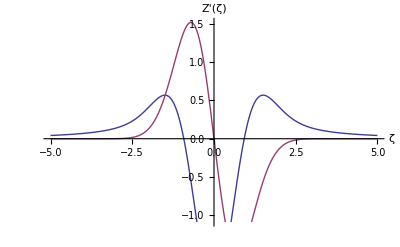

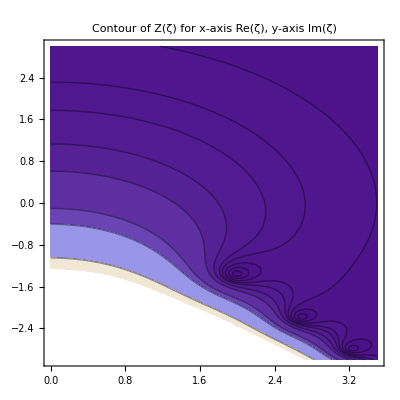

```mathematica
fHz=1.15 10^8;
kPer=0;
vPhs=w/kPar;
λ=2 Pi /kPar;
w=2 Pi fHz;
ne=1.1 10^14;
b0=0.0001;
amuZ=-1;
me=9.10938188 10^-31;
ee=1.602 10^-19;
e0=8.854187817 10^-12;
kPar=22.11;
vThHere[EeV_]:=Sqrt[2 EeV ee/me];

LogLinearPlot[{Re[sig33[vThHere[EeV],w,e0,kPar,ne,me,-ee]],Im[sig33[vThHere[EeV],w,e0,kPar,ne,me,-ee]]},{EeV,100,10000},Filling->Axis,AxesLabel->{Energy [eV],σ33}]
Plot[{Re[Z[x]],Im[Z[x]]},{x,-5,5},AxesLabel->{"ζ","Z(ζ)"}]
Plot[{Re[Zp[x]],Im[Zp[x]]},{x,-5,5},AxesLabel->{"ζ","Z'(ζ)"}]
ContourPlot[Abs[Z[x+I y]],{x,0,3.5},{y,-3.0,3.0},Contours->{0.1,0.2,0.3,0.4,0.5,0.7,1.0,2.0,3.0,10.0,100.0},PlotLabel->"Contour of Z(ζ) for x-axis Re(ζ), y-axis Im(ζ)"]
tValsZ={100,200,300,500,800,1000,1500,2000,3000,4000,5000,6000,7000,10000};
reValsZ= Table[{rteV,Re[sig33[vThHere[rteV],w,e0,kPar,ne,me,-ee]]},{rteV,tValsZ}];
imValsZ= Table[{rteV,Im[sig33[vThHere[rteV],w,e0,kPar,ne,me,-ee]]},{rteV,tValsZ}];
```

Analytic, per v current calculation

```mathematica
x[v_,t_]:=v t;
eField[v_,t_,phs_,E0_]:= E0 Exp[-I (k x[v,t]+ω t+phs)];
v1[v_,phs_,nRF_,rfPeriod_,E0_]=q/m Integrate[eField[v,t,phs,E0],{t,-nRF rfPeriod,0}]
v1Indef[v_,phs_,E0_]=q/m Integrate[eField[v,t,phs,E0],{t,-Infinity,0},Assumptions->{k∈Reals,v∈Reals,Im[ω]>0}]
f[v_,vTh_,n_]:= n/(vTh Sqrt[Pi]) Exp[-v^2/vTh^2];
j[n_,vTh_,phs_,nRF_,rfPeriod_,E0_]:=q NIntegrate[(v+v1[v,phs,nRF,rfPeriod,E0]) f[v,vTh,n],{v,-3 vTh,3 vTh}]
jIndef[n_,vTh_,phs_,E0_]=q Integrate[(v+v1Indef[v,phs,E0]) f[v,vTh,n],{v,-Infinity,Infinity},Assumptions->{k∈Reals,v∈Reals,Im[ω]>0,Re[ω]>0,vTh∈Reals,vTh>0,Abs[k]>0}]
sig33Dlg=FullSimplify[jIndef[n,vTh,0,1],Assumptions->{Im[k/ω]>0}]
```

-(ⅈ ⅇ^(-ⅈ phs) (-1+ⅇ^(ⅈ nRF rfPeriod (k v+ω))) E0 q)/(m (k v+ω))

(ⅈ ⅇ^(-ⅈ phs) E0 q)/(m (k v+ω))

(ⅈ ⅇ^(-ⅈ phs-ω^2/(k^2 vTh^2)) E0 n q^2 (π Erfi[ω/(k vTh)]-Log[-k/ω]+Log[k/ω]))/(k m √π vTh)

(ⅈ ⅇ^(-ω^2/(k^2 vTh^2)) n √π q^2 (ⅈ+Erfi[ω/(k vTh)]))/(k m vTh)

```mathematica
sig33[vTh,ω,ϵ0,k,n,m,q]
FullSimplify[ sig33Dlg/sig33[vTh,ω,ϵ0,k,n,m,q],,Assumptions->{k∈Reals,v∈Reals,Im[ω]>0,Re[ω]>0,vTh∈Reals,vTh>0,Abs[k]>0,Im[k/ω]>0}]
```

-(2 ⅈ n q^2 ω (k vTh+ⅈ ⅇ^(-ω^2/(k^2 vTh^2)) √π ω Erfc[-(ⅈ ω)/(k vTh)]))/(k^3 m vTh^3)

-(k^2 √π vTh^2 (ⅈ+Erfi[ω/(k vTh)]))/(2 ω (ⅇ^(ω^2/(k^2 vTh^2)) k vTh+ⅈ √π ω Erfc[-(ⅈ ω)/(k vTh)]))

```mathematica
-I ω/(k vTh) /I
1/I
```

-ω/(k vTh)

-ⅈ

```mathematica
FullSimplify[-Log[-a]+Log[a],Assumptions->Im[a]>0]
```

```mathematica
eCharge=1.60217646 10^-19; m=9.10938188 10^-31;
q=-eCharge;
freq=1.15 10^8;
E0=5000;
rfPeriod=1/freq;
someeV=500;
vTh[someeV_]:=Sqrt[2 someeV eCharge/m];
n=1.1 10^14;
k = 22.11;
nRF =5;
ω=2 Pi freq +I 2 Pi freq 1 10^-6;
vvv[teV_]:=Sign[teV]Sqrt[2 Abs[teV] eCharge/ m];
vPhs=Re[ω/k];tPhs=0.5 m vPhs^2/eCharge;
```

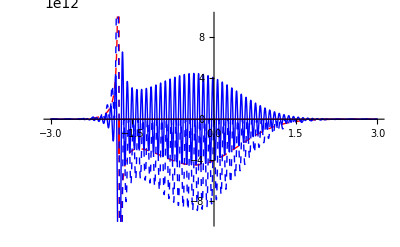

```mathematica
tPhs=0.00rfPeriod ;
thisE=1000;
thisnRF=20;
Needs["PlotLegends`"]
Plot[{Re[v1Indef[v vTh[thisE],tPhs,E0]f[v vTh[thisE],vTh[thisE],n]] ,
Im[v1Indef[v vTh[thisE],tPhs,E0]f[v vTh[thisE],vTh[thisE],n]],
Re[v1[v vTh[thisE],tPhs/rfPeriod 2 π,thisnRF,rfPeriod,E0]f[v vTh[thisE],vTh[thisE],n]],Im[v1[v vTh[thisE],tPhs/rfPeriod 2 π,thisnRF,rfPeriod,E0]f[v vTh[thisE],vTh[thisE],n]]},{v,-3 ,3 },PlotStyle->{Directive[Red,Thick],Directive[Red,Dashed,Thick],Blue,Directive[Blue,Dashed]},PlotRange->0.1 10^14]
```

```mathematica
NIntegrate[ f[v,vTh[500],n],{v,-3 vTh[500],3 vTh[500]}]
```

1.09998×10^14

```mathematica
thisE=10000;
j[n,vTh[thisE],0.1 2 Pi,5,rfPeriod,E0]
jIndef[n,vTh[thisE],0.1 2 Pi,E0]
```

18.789-0.446495 ⅈ

18.789-0.44651 ⅈ

4045.08+2938.93 ⅈ

2.54664×10^7+50.9328 ⅈ

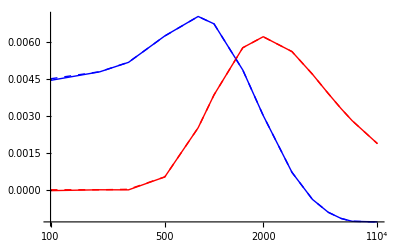

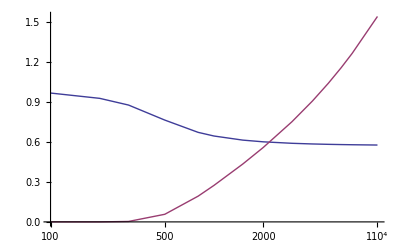

```mathematica
tVals={100,200,300,500,800,1000,1500,2000,3000,4000,5000,6000,7000,10000};
thisPhs=0.9 2 Pi;
thisnRF =5;
eField[0,0,thisPhs,E0]
ω^2/(k^2 vTh[5000])

reVals= Table[{rteV,
Re[((j[n,vTh[rteV],thisPhs,thisnRF,rfPeriod,E0]/eField[0,0,thisPhs,E0] )-I n q^2/(m ω))2 ω^2/(k^2 vTh[rteV]^2)]},{rteV,tVals}];
imVals=Table[{rteV,
Im[((j[n,vTh[rteV],thisPhs,thisnRF,rfPeriod,E0]/eField[0,0,thisPhs,E0])-I n q^2/(m ω))2 w^2/(k^2 vTh[rteV]^2)]},{rteV,tVals}];
ListLogLinearPlot[{reVals,imVals,reValsZ,imValsZ},PlotStyle->{Red,Blue,Directive[Red,Dashed],Directive[Blue,Dashed]},Joined->True]
ratioRe=Table[{rteV,Re[(j[n,vTh[rteV],thisPhs,thisnRF,rfPeriod,E0]/eField[0,0,thisPhs,E0])/sig33[vTh[rteV],w,e0,kPar,ne,me,-ee]]},{rteV,tVals}];
ratioIm=Table[{rteV,Im[(j[n,vTh[rteV],thisPhs,thisnRF,rfPeriod,E0]/eField[0,0,thisPhs,E0])/sig33[vTh[rteV],w,e0,kPar,ne,me,-ee]]},{rteV,tVals}];
ListLogLinearPlot[{ratioRe,ratioIm},Joined->True]
```

```mathematica
(*LogLinearPlot[{Re[j[n,vTh[rteV],0,nRF,rfPeriod,E0]/E0],Im[j[n,vTh[rteV],0,nRF,rfPeriod,E0]/E0]},{rteV,100,10000},PlotPoints->10]*)
(*Plot3D[Re[eField[v vPhs,t,0,E0]],{t,0,-nRF rfPeriod},{v,-2,0},PlotRange->Full,PlotPoints->40]
Plot3D[Re[v1[v[teV],phs,nRF,rfPeriod,E0]],{phs,0,2 Pi},{teV,-2tPhs,0},ColorFunction->"RustTones"]*)
```